```mathematica
triangle={
{75},
{95,64},
{17,47,82},
{18,35,87,10},
{20,04,82,47,65},
{19,01,23,75,03,34},
{88,02,77,73,07,63,67},
{99,65,04,28,06,16,70,92},
{41,41,26,56,83,40,80,70,33},
{41,48,72,33,47,32,37,16,94,29},{53,71,44,65,25,43,91,52,97,51,14},{70,11,33,28,77,73,17,78,39,68,17,57},{91,71,52,38,17,14,91,43,58,50,27,29,48},{63,66,04,68,89,53,67,30,73,16,69,87,40,31},{04,62,98,27,23,09,70,98,73,93,38,53,60,04,23}};
```

```mathematica
(* This function chooses the bigger value between two options in a given row at a given index.  It also returns the index {biggestvalue, index in row} *)
getBigVal[row_,i_]:=First[TakeLargest[{triangle[[row]][[i]],triangle[[row]][[i+1]]},1]]

getValPos[row_,i_]:=Select[Flatten[Position[triangle[[row]],getBigVal[row,i]]],#≥i&][[1]]

bigger[row_,i_]:={getBigVal[row,i],getValPos[row,i]}
(*  end above section *)

(* below is a function with module that does all the previous parts *)
findBigger[row0_,i0_]:=
Module[{row = row0,i=i0,val,pos,result},
val=First[TakeLargest[{triangle[[row]][[i]],triangle[[row]][[i+1]]},1]];
pos=Select[Flatten[Position[triangle[[row]],getBigVal[row,i]]],#≥i&][[1]];
result={val,pos};
result
]
```

```mathematica
(* this function with module calculates the first path from top to bottom *)
pDown[rows0_]:=
Module[{rows=rows0,path={75},pos=1},
For[i=2,i<=rows,i++,temp=findBigger[i,pos];
pos=temp[[2]];
AppendTo[path,temp[[1]]]
];
path
]
pDown[15]
```

{75,95,47,87,82,75,73,28,83,47,43,73,91,67,98}

```mathematica
filterTriangle[rows0_]:=
Module[{rows=rows0,maxes=pDown[15],newTriangle=triangle,i},
For[i=1,i≤rows,i++,
newTriangle[[i]]=Function[x,x-maxes[[i]]]/@newTriangle[[i]]];
newTriangle//TableForm
]

filterTriangle[15]
triangle //TableForm
```

0 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | -31 |  |  |  |  |  |  |  |  |  |  |  |  | 
-30 | 0 | 35 |  |  |  |  |  |  |  |  |  |  |  | 
-69 | -52 | 0 | -77 |  |  |  |  |  |  |  |  |  |  | 
-62 | -78 | 0 | -35 | -17 |  |  |  |  |  |  |  |  |  | 
-56 | -74 | -52 | 0 | -72 | -41 |  |  |  |  |  |  |  |  | 
15 | -71 | 4 | 0 | -66 | -10 | -6 |  |  |  |  |  |  |  | 
71 | 37 | -24 | 0 | -22 | -12 | 42 | 64 |  |  |  |  |  |  | 
-42 | -42 | -57 | -27 | 0 | -43 | -3 | -13 | -50 |  |  |  |  |  | 
-6 | 1 | 25 | -14 | 0 | -15 | -10 | -31 | 47 | -18 |  |  |  |  | 
10 | 28 | 1 | 22 | -18 | 0 | 48 | 9 | 54 | 8 | -29 |  |  |  | 
-3 | -62 | -40 | -45 | 4 | 0 | -56 | 5 | -34 | -5 | -56 | -16 |  |  | 
0 | -20 | -39 | -53 | -74 | -77 | 0 | -48 | -33 | -41 | -64 | -62 | -43 |  | 
-4 | -1 | -63 | 1 | 22 | -14 | 0 | -37 | 6 | -51 | 2 | 20 | -27 | -36 | 
-94 | -36 | 0 | -71 | -75 | -89 | -28 | 0 | -25 | -5 | -60 | -45 | -38 | -94 | -75

75 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
95 | 64 |  |  |  |  |  |  |  |  |  |  |  |  | 
17 | 47 | 82 |  |  |  |  |  |  |  |  |  |  |  | 
18 | 35 | 87 | 10 |  |  |  |  |  |  |  |  |  |  | 
20 | 4 | 82 | 47 | 65 |  |  |  |  |  |  |  |  |  | 
19 | 1 | 23 | 75 | 3 | 34 |  |  |  |  |  |  |  |  | 
88 | 2 | 77 | 73 | 7 | 63 | 67 |  |  |  |  |  |  |  | 
99 | 65 | 4 | 28 | 6 | 16 | 70 | 92 |  |  |  |  |  |  | 
41 | 41 | 26 | 56 | 83 | 40 | 80 | 70 | 33 |  |  |  |  |  | 
41 | 48 | 72 | 33 | 47 | 32 | 37 | 16 | 94 | 29 |  |  |  |  | 
53 | 71 | 44 | 65 | 25 | 43 | 91 | 52 | 97 | 51 | 14 |  |  |  | 
70 | 11 | 33 | 28 | 77 | 73 | 17 | 78 | 39 | 68 | 17 | 57 |  |  | 
91 | 71 | 52 | 38 | 17 | 14 | 91 | 43 | 58 | 50 | 27 | 29 | 48 |  | 
63 | 66 | 4 | 68 | 89 | 53 | 67 | 30 | 73 | 16 | 69 | 87 | 40 | 31 | 
4 | 62 | 98 | 27 | 23 | 9 | 70 | 98 | 73 | 93 | 38 | 53 | 60 | 4 | 23

```mathematica
Style[#,Red]&/@triangle
```

```mathematica
tester={-2,3,5-11,15}
tester=If[#>0,Style[#,Red],Style[#,Black]]&/@tester
colorValues[rows0_]:=
Module[{rows=rows0},
For[i=1,i≤rows,i++,
newTriangle[[i]]=If[#>0,Style[#,Red],Style[#,Black]]&/@newTriangle[[i]]
];
newTriangle//TableForm
]
colorValues[15]
```

{-2,3,-6,15}

{-2,3,-6,15}

0 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | -31 |  |  |  |  |  |  |  |  |  |  |  |  | 
-30 | 0 | 35 |  |  |  |  |  |  |  |  |  |  |  | 
-69 | -52 | 0 | -77 |  |  |  |  |  |  |  |  |  |  | 
-62 | -78 | 0 | -35 | -17 |  |  |  |  |  |  |  |  |  | 
-56 | -74 | -52 | 0 | -72 | -41 |  |  |  |  |  |  |  |  | 
15 | -71 | 4 | 0 | -66 | -10 | -6 |  |  |  |  |  |  |  | 
71 | 37 | -24 | 0 | -22 | -12 | 42 | 64 |  |  |  |  |  |  | 
-42 | -42 | -57 | -27 | 0 | -43 | -3 | -13 | -50 |  |  |  |  |  | 
-6 | 1 | 25 | -14 | 0 | -15 | -10 | -31 | 47 | -18 |  |  |  |  | 
10 | 28 | 1 | 22 | -18 | 0 | 48 | 9 | 54 | 8 | -29 |  |  |  | 
-3 | -62 | -40 | -45 | 4 | 0 | -56 | 5 | -34 | -5 | -56 | -16 |  |  | 
0 | -20 | -39 | -53 | -74 | -77 | 0 | -48 | -33 | -41 | -64 | -62 | -43 |  | 
-4 | -1 | -63 | 1 | 22 | -14 | 0 | -37 | 6 | -51 | 2 | 20 | -27 | -36 | 
-94 | -36 | 0 | -71 | -75 | -89 | -28 | 0 | -25 | -5 | -60 | -45 | -38 | -94 | -75

```mathematica
tester
```

{-2,3,-6,15}

```mathematica
firstFive={{75},
{95,64},
{17,47,82},
{18,35,87,10},
{20,04,82,47,65}};
firstFive //MatrixForm
```

({75}
{95,64}
{17,47,82}
{18,35,87,10}
{20,4,82,47,65})

// Ignore the top item
L,L,L,L		R,R,R,R	// Edges
L,L,L,R		R,R,R,L	// Edges until last one

L,L,R,L		R,R,L,R	// middles
L,L,R,R	R,R,L,L

L,R,L,L		R,L,R,R
L,R,L,R	R,L,R,L

L,R,R,L	R,L,L,R	
L,R,R,R	R,L,L,L

```mathematica
Clear[a,b];
a=firstFive[[1]]
b=firstFive[[2]]
c=firstFive[[3]][[1;;2]]
d=firstFive[[4]]
Subsets[firstFive[[5]]];
```

{75}

{95,64}

{17,47}

{18,35,87,10}

Rules for picking a value in a path
1. Pick one value per row
2. Move to next row
3. Pick value with same index as row item above, or index + 1
4. Repeat step 3 until at end

```mathematica
firstFive //TableForm
pick[list_,row_,i_]:=First[TakeLargest[{list[[row+1]][[i]],list[[row+1]][[i+1]]},1]]
pick[firstFive,4,4]
```

75 |  |  |  | 
95 | 64 |  |  | 
17 | 47 | 82 |  | 
18 | 35 | 87 | 10 | 
20 | 4 | 82 | 47 | 65

47

```mathematica
a=firstFive[[2]];
b=firstFive[[3]];
Length[Permutations[Flatten[{a,b}]]];
TreePlot[{1->2,1->3,2->4,2->5,3->5,3->6},VertexLabeling->True];

BooleanTable[
```

120

```mathematica
paths={}

For[j=1,j≤2^4,j++,
cPath={};
For[i=1,i≤5,i++,
cPath=AppendTo[cPath,firstFive[[i]][[1]]]
];
paths=AppendTo[paths,cPath]
]
paths
```

{}

{{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20},{75,95,17,18,20}}

```mathematica
triangle={
{75},
{95,64},
{17,47,82},
{18,35,87,10},
{20,04,82,47,65},
{19,01,23,75,03,34},
{88,02,77,73,07,63,67},
{99,65,04,28,06,16,70,92},
{41,41,26,56,83,40,80,70,33},
{41,48,72,33,47,32,37,16,94,29},
{53,71,44,65,25,43,91,52,97,51,14},{70,11,33,28,77,73,17,78,39,68,17,57},{91,71,52,38,17,14,91,43,58,50,27,29,48},{63,66,04,68,89,53,67,30,73,16,69,87,40,31},{04,62,98,27,23,09,70,98,73,93,38,53,60,04,23}};
```

```mathematica
relations={75<->95,75<->64,95<->17,95<->47,64<->47,64<->82};
tThree=Graph[relations,VertexLabels->"Name"];
FindPath[tThree,75,47,Infinity,All];
Length[triangle[[15]]];
```

{}

{95→17,95→47,17→18,17→35,47→35,47→87,18→20,18→4,35→4,35→82,87→82,87→47,20→19,20→1,4→1,4→23,82→23,82→75,47→75,47→3,19→88,19→2,1→2,1→77,23→77,23→73,75→73,75→7,3→7,3→63,88→99,88→65,2→65,2→4,77→4,77→28,73→28,73→6,7→6,7→16,63→16,63→70,99→41,99→41,65→41,65→26,4→26,4→56,28→56,28→83,6→83,6→40,16→40,16→80,70→80,70→70,41→41,41→48,41→48,41→72,26→72,26→33,56→33,56→47,83→47,83→32,40→32,40→37,80→37,80→16,70→16,70→94,41→53,41→71,48→71,48→44,72→44,72→65,33→65,33→25,47→25,47→43,32→43,32→91,37→91,37→52,16→52,16→97,94→97,94→51,53→70,53→11,71→11,71→33,44→33,44→28,65→28,65→77,25→77,25→73,43→73,43→17,91→17,91→78,52→78,52→39,97→39,97→68,51→68,51→17,70→91,70→71,11→71,11→52,33→52,33→38,28→38,28→17,77→17,77→14,73→14,73→91,17→91,17→43,78→43,78→58,39→58,39→50,68→50,68→27,17→27,17→29,91→63,91→66,71→66,71→4,52→4,52→68,38→68,38→89,17→89,17→53,14→53,14→67,91→67,91→30,43→30,43→73,58→73,58→16,50→16,50→69,27→69,27→87,29→87,29→40}

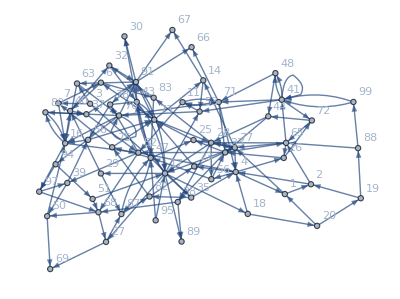

```mathematica
rels={}
For[i=1,i<14,i++,
For[j=1,j<Length[triangle[[i]]],j++,
AppendTo[rels,triangle[[i]][[j]]-> triangle[[i+1]][[j]]];
AppendTo[rels,triangle[[i]][[j]]-> triangle[[i+1]][[j+1]]]
]
]
rels
gRels=Graph[rels,VertexLabels->"Name"]
```

```mathematica
triangle[[3]]
newTri=triangle[[3]]/.#->1&
```

{17,47,82}

triangle⟦3⟧/.#1→1&

```mathematica
#->1&/@triangle[[3]]
```

{17→1,47→1,82→1}

```mathematica
triangle[[3]]/.17->1
```

{100.,276.471,482.353}→1

```mathematica
triangle //TableForm
```

75 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
95 | 64 |  |  |  |  |  |  |  |  |  |  |  |  | 
17 | 47 | 82 |  |  |  |  |  |  |  |  |  |  |  | 
18 | 35 | 87 | 10 |  |  |  |  |  |  |  |  |  |  | 
20 | 4 | 82 | 47 | 65 |  |  |  |  |  |  |  |  |  | 
19 | 1 | 23 | 75 | 3 | 34 |  |  |  |  |  |  |  |  | 
88 | 2 | 77 | 73 | 7 | 63 | 67 |  |  |  |  |  |  |  | 
99 | 65 | 4 | 28 | 6 | 16 | 70 | 92 |  |  |  |  |  |  | 
41 | 41 | 26 | 56 | 83 | 40 | 80 | 70 | 33 |  |  |  |  |  | 
41 | 48 | 72 | 33 | 47 | 32 | 37 | 16 | 94 | 29 |  |  |  |  | 
53 | 71 | 44 | 65 | 25 | 43 | 91 | 52 | 97 | 51 | 14 |  |  |  | 
70 | 11 | 33 | 28 | 77 | 73 | 17 | 78 | 39 | 68 | 17 | 57 |  |  | 
91 | 71 | 52 | 38 | 17 | 14 | 91 | 43 | 58 | 50 | 27 | 29 | 48 |  | 
63 | 66 | 4 | 68 | 89 | 53 | 67 | 30 | 73 | 16 | 69 | 87 | 40 | 31 | 
4 | 62 | 98 | 27 | 23 | 9 | 70 | 98 | 73 | 93 | 38 | 53 | 60 | 4 | 23

```mathematica
firstFive={{75},
{95,64},
{17,47,82},
{18,35,87,10},
{20,04,82,47,65}};
firstFive //TableForm
```

75 |  |  |  | 
95 | 64 |  |  | 
17 | 47 | 82 |  | 
18 | 35 | 87 | 10 | 
20 | 4 | 82 | 47 | 65

I need to create an algorithm that will list out all the possible combinations. I can use this to calculate all the paths...

// Ignore the top item
L,L,L,L		R,R,R,R	// Edges
L,L,L,R		R,R,R,L	// Edges until last one

L,L,R,L		R,R,L,R	// middles
L,L,R,R	R,R,L,L

L,R,L,L		R,L,R,R
L,R,L,R	R,L,R,L

L,R,R,L	R,L,L,R	
L,R,R,R	R,L,L,L		

{75}
{75,95}					  {75,64}  
{75,95,17}	{75,95,47}	  {75,64,47} 	{75,64,82}

{1,1}
{{1,1},{2,1}}	{{1,1},{2,2}}
{{1,1},{2,1},{3,1}}	{{1,1},{2,1},{3,2}}	{{1,1},{2,2},{3,2}}	{{1,1},{2,2},{3,3}}

In each new row, a path is replaced by two new paths

Row 1: Make new path {75}  				1 Path		2^0
Row 2: Make two paths for each previous path	2 Paths	2^1
Row 3: Make two paths for each previous path	4 Paths	2^2
Row 4: Make two paths for each previous path	8 Paths	2^3
Row 5: Make two paths for each previous path	16 Paths	2^4

```mathematica
(*  ROW 1 *)
paths={};
AppendTo[paths,{75}];
item[row_,col_]:=triangle[[row]][[col]]
pItem[n_]:=paths[[n]]

(* ROW 2   1-1 *)
AppendTo[paths,Append[pItem[1],item[2,1]]];
AppendTo[paths,Append[pItem[1],item[2,2]]];
paths=Select[paths,Length[#]≥2&,Infinity];

(* ROW 3  1-2-1 *)
AppendTo[paths,Append[pItem[1],item[3,1]]];

AppendTo[paths,Append[pItem[1],item[3,2]]];
AppendTo[paths,Append[pItem[2],item[3,2]]];

AppendTo[paths,Append[pItem[2],item[3,3]]];
paths=Select[paths,Length[#]≥3&,Infinity];

(* ROW 4   1-3-3-1 *)
AppendTo[paths,Append[pItem[1],item[4,1]]];

AppendTo[paths,Append[pItem[1],item[4,2]]];
AppendTo[paths,Append[pItem[2],item[4,2]]];
AppendTo[paths,Append[pItem[3],item[4,2]]];

AppendTo[paths,Append[pItem[2],item[4,3]]];
AppendTo[paths,Append[pItem[3],item[4,3]]];
AppendTo[paths,Append[pItem[4],item[4,3]]];

AppendTo[paths,Append[pItem[4],item[4,4]]];
paths=Select[paths,Length[#]≥4&,Infinity];

(* ROW 5 1-4-6-4-1 *)

AppendTo[paths,Append[pItem[1],item[5,1]]];

AppendTo[paths,Append[pItem[1],item[5,2]]];
AppendTo[paths,Append[pItem[2],item[5,2]]];
AppendTo[paths,Append[pItem[3],item[5,2]]];
AppendTo[paths,Append[pItem[4],item[5,2]]];

AppendTo[paths,Append[pItem[2],item[5,3]]];
AppendTo[paths,Append[pItem[3],item[5,3]]];
AppendTo[paths,Append[pItem[4],item[5,3]]];
AppendTo[paths,Append[pItem[5],item[5,3]]];
AppendTo[paths,Append[pItem[6],item[5,3]]];
AppendTo[paths,Append[pItem[7],item[5,3]]];

AppendTo[paths,Append[pItem[5],item[5,4]]];
AppendTo[paths,Append[pItem[6],item[5,4]]];
AppendTo[paths,Append[pItem[7],item[5,4]]];
AppendTo[paths,Append[pItem[8],item[5,4]]];

AppendTo[paths,Append[pItem[8],item[5,5]]];



paths=Select[paths,Length[#]≥5&,Infinity];
paths
Total/@paths
Max[Total/@paths]
```

{{75,95,17,18,20},{75,64,82,10,65},{75,95,17,18,4},{75,95,17,35,4},{75,95,47,35,4},{75,64,47,35,4},{75,95,17,35,82},{75,95,47,35,82},{75,64,47,35,82},{75,95,47,87,82},{75,64,47,87,82},{75,64,82,87,82},{75,95,47,87,47},{75,64,47,87,47},{75,64,82,87,47},{75,64,82,10,47}}

{225,296,209,226,256,225,304,334,303,386,355,390,351,320,355,278}

390

```mathematica
firstFive//TableForm
```

75 |  |  |  | 
95 | 64 |  |  | 
17 | 47 | 82 |  | 
18 | 35 | 87 | 10 | 
20 | 4 | 82 | 47 | 65